```mathematica
(*Задание 1*)
```

```mathematica
f[x_]:=14 x^3-179 x^2+281x-66;
Plot[f[x],{x,-1,12},AxesOrigin->{0,0},ImageSize->Small]
```

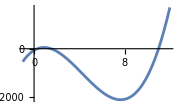

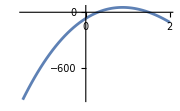

```mathematica
Plot[f[x],{x,-1.5,2},AxesOrigin->{0,0},ImageSize->Small]
```

```mathematica
(*По графикам видно,что уравнение имеет три действительных корня.Они
расположены в интервалах(0,0.5),(1,1.5),(10.5,11.5)*)
```

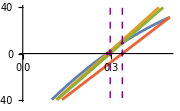

Решение х= 0.286236 Шаг= 4

```mathematica
a = 0 ;
b = 0.5;
eps = 0.001;
ex = eps*10;
If[f[a]*f''[a]>0,
x0=b;
g[x_]:=a-(f[a]*(x-a))/(f[x]-f[a]);
horda[x_,xn_]:=f[xn]+((x-xn)*(f[xn]-f[a]))/(xn-a),
x0=a;
g[x_]:=x-(f[x]*(b-x))/(f[b]-f[x]);
horda[x_,xn_]:=
f[xn]+((x-xn)*(f[xn]-f[b]))/(xn-b);
]
x1=g[x0];
n=1;
While[ex>eps,If[n==2,Print[Plot[{f[x],horda[x,x1],horda[x,x0],horda[x,x01]},{x,a,b},
Epilog->{Purple,Dashed,InfiniteLine[{x1,0},{0,1}],InfiniteLine[{x0,0},{0,1}],PointSize[0.013],Point[{{x0,0},{x0,f[x0]},{x1,0},{x1,f[x1]},{g[x1],0}}]},PlotRange->40]]];
x01=x0;x0=x1;
x1=g[x0];
ex=(x1-x0)^2/Abs[x1+x01-2 x0];
n=n+1;]
Print["Решение х= ",x1//N," Шаг= ",n
]
```

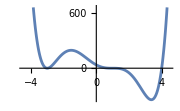

```mathematica
(*Задание 2*)
f2[x_]=x^6-x^5-18 x^4+14 x^3+61 x^2-93x+36;
Plot[f2[x],{x,-4.5,4.5},AxesOrigin->{0,0},ImageSize->Small]
```

```mathematica
(*Корни данного уравнения находятся на промежутках (-3.5;-2.5),(0.5,1.5),(3.5;4.5)*)
```

```mathematica
Solve[f2[x]==0]
```

{{x→-3},{x→-3},{x→1},{x→1},{x→1},{x→4}}

```mathematica
NSolve[f2[x]==0]
```

{{x→-3.},{x→-3.},{x→1.},{x→1.},{x→1.},{x→4.}}

```mathematica
Roots[f2[x]==0,x]
```

x==-3||x==-3||x==1||x==1||x==1||x==4

```mathematica
Factor[f2[x]]
```

(-4+x) (-1+x)^3 (3+x)^2

```mathematica
FindRoot[f2[x]==0,{x,5}]
```

{x→4.}

```mathematica
FindRoot[f2[x]==0,{x,0.5}]
```

{x→0.999997}

```mathematica
FindRoot[f2[x]==0,{x,-3.5}]
```

{x→-3.}

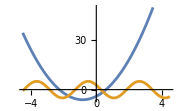

```mathematica
(*Задание 3*)
f3[x_]=5Cos[2x+1];
g3[x_]=3 x^2+5x-4;
Plot[{g3[x],f3[x]},{x,-4.5,4.5},AxesOrigin->{0,0},ImageSize->Small]
```

```mathematica
(*Корни данного уравнения находятся на промежутках (-2,-1),(0,0.5)*)
```

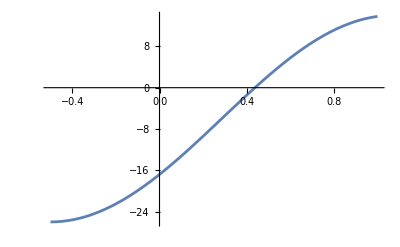

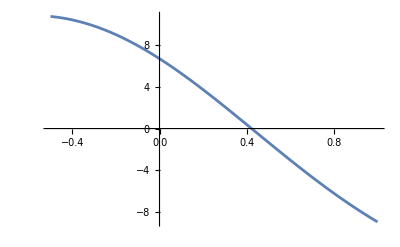

-3.09121

-112.626

Решение х = 0.422147 получено на 2 шаге.

```mathematica
f4[x_]=5Cos[2x+1]-3 x^2-5x+4;
Plot[f4''[x],{x,-0.5,1}]
Plot[f4[x],{x,-0.5,1}]
b=0.5;
a=0;
eps=0.001;
f4[b]*f4''[b]//N
f4[a]*f4''[a]//N
xn1=b;
Do[xn2=xn1;
xn1=(xn1-f4[xn1]/f4'[xn1])//N;
If[Abs[xn2-xn1]<eps,
Print["Решение х = ",xn2//N, 
" получено на ",n," шаге."];
Break[]],
{n,1,100}]
```

```mathematica
a=-2;
b=-1.5;
eps=0.001;
xn1=a;
xn2=b;
Do[xn3=xn2;
xn2=xn2-(xn2-xn1)/(f4[xn2]-f4[xn1])*f4[xn2]//N;
If[Abs[xn3-xn2]<eps,
Print["Решение х = ",xn3//N, 
" получено на ",n," шаге."];
Break[]],
{n,1,100}]
```

Решение х = -1.71266 получено на 4 шаге.

```mathematica
(*Задание 4*)
a=0;
b = 0.5;
eps=0.001;
f4[x_]=5Cos[2x+1]-3 x^2-5x+4;
λ = 1/MaxValue[{Abs[f4'[x]],a<=x<=b},x];
φ[x_] = x+λ*f4[x];
xn1= a;
Do[xn2=xn1;
xn1=φ[xn1]//N;
If[Abs[xn1-xn2]<eps,
Print["Решение х = ",xn1//N, 
" получено на ",n," шаге."];
Break[]],
{n,1,1000}]
```

Решение х = 0.422388 получено на 3 шаге.

```mathematica
a=-2;
b = -1.5;
eps=0.001;
f4[x_]=5Cos[2x+1]-3 x^2-5x+4;
λ = 1/MaxValue[{Abs[f4'[x]],a<=x<=b},x];
φ[x_] = x-λ*f4[x];
xn1= a;
Do[xn2=xn1;
xn1=φ[xn1]//N;
If[Abs[xn1-xn2]<eps,
Print["Решение х = ",xn2//N, 
" получено на ",n," шаге."];
Break[]],
{n,1,1000}]
```

Решение х = -1.71274 получено на 4 шаге.

```mathematica
(*Задание 5*)
NSolve[f4[x]==0,Reals]
```

{{x→-1.71202},{x→0.422388}}

```mathematica
FindRoot[f4[x]==0,{x,0.5}]
```

{x→0.422388}

```mathematica
FindRoot[f4[x]==0,{x,-1.5}]
```

{x→-1.71202}

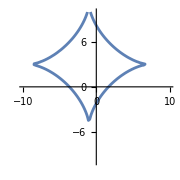

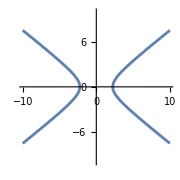

```mathematica
(*Задание 6*)
g1[x_,y_]=((x+1)^2)^(1/3)+((y-3)^2)^(1/3)-4;
g2[x_,y_]=3 x^2-5 y^2-15;
gr1= ContourPlot[g1[x,y]==0, {x,-10,10},{y,-10,10}, Axes->True, Frame->False,ImageSize->Small]
gr2 = ContourPlot[g2[x,y]==0, {x,-10,10},{y,-10,10}, Axes->True, Frame->False,ImageSize->Small]
```

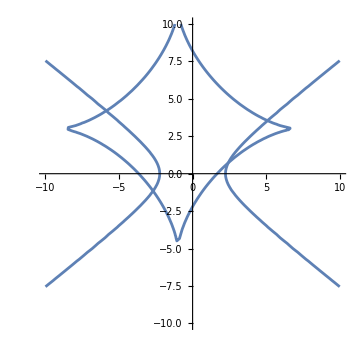

```mathematica
Show[gr1, gr2, ImageSize->Medium]
```

```mathematica
FindRoot[{g1[x,y]==0,g2[x,y]==0}, {x,-7},{y,4}]
```

{x→-5.86466,y→4.19959}

```mathematica
FindRoot[{g1[x,y]==0,g2[x,y]==0}, {x,-3},{y,-1}]
```

{x→-2.68587,y→-1.15253}

```mathematica
FindRoot[{g1[x,y]==0,g2[x,y]==0}, {x,5},{y,4}]
```

{x→5.09045,y→3.54226}

```mathematica
FindRoot[{g1[x,y]==0,g2[x,y]==0}, {x,2},{y,1}]
```

{x→2.42671,y→0.730304}

```mathematica
NSolve[{g1[x,y]==0,g2[x,y]==0},Reals]
```

{{x→5.09045,y→3.54226},{x→-2.68587,y→-1.15253},{x→-5.86466,y→4.19959},{x→2.42671,y→0.730304}}